# Вариант 5

### 1

```mathematica
a=0.1;
L=1;
dh=0.01;
n=IntegerPart[L/dh*6];
τ=0.1;
smax=300;
H[x_]=Cos[2π x/L]+1;
h0[x_]=Sin[4π x/L]+1;
Q[x_,t_]=Abs[Cos[20*t]]*Exp[-50*(x-3*L)^2];
Clear[h]
For[i=0;,i≤n,i++,h[i,0]=h0[dh*i]]
For[s=0,s≤smax,s++,h[0,s]=0;h[n,s]=0]
Clear[s]
eqn[s_]:=Table[(h[i,s+1]-h[i,s])/τ==a*((H[dh*(i+1/2)]+(h[i,s]+h[i+1,s])/2)(h[i+1,s+1]-h[i,s+1])/dh^2-(H[(i-1/2)*dh]+(h[i,s]+h[i-1,s])/2)(h[i,s+1]-h[i-1,s+1])/dh^2),{i,1,n-1}]
Y[s_]:=Table[h[i,s],{i,1,n-1}]
```

### 2

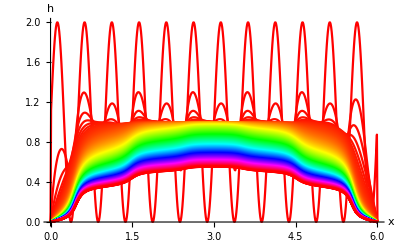

```mathematica
For[s=0,s≤ smax,s++,{B,A}=CoefficientArrays[eqn[s],Y[s+1]];
yy=LinearSolve[A,-B];
Do[h[i,s+1]=yy[[i]],{i,1,n-1}]]
Show[Table[ListPlot[Table[{i*dh,h[i,s]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax]],{s,0,smax}],PlotRange->Automatic,AxesLabel->{"x","h"}]
```

### 3

```mathematica
Clear[eqn2,c,Y2,yy2,A,B]
 For[i=0;,i≤n,i++,c[i,0]=0];
For[s=0,s≤smax,s++,c[0,s]=0;c[n,s]=0];
Clear[s]
eqn2[s_]:=Table[(c[i,s+1]*(H[dh*i]+h[i,s+1])-c[i,s]*(H[dh*i]+h[i,s]))/τ==a*(((c[i+1,s+1]+c[i,s+1])/2*((h[i+1,s+1]+h[i,s+1])/2+H[dh*(i+1/2)]))(h[i+1,s+1]-h[i,s+1])/dh^2-((c[i,s+1]+c[i-1,s+1])/2*((h[i-1,s+1]+h[i,s+1])/2+H[dh*(i-1/2)]))(h[i,s+1]-h[i-1,s+1])/dh^2)+Q[i*dh,s*τ],{i,1,n-1}]
Y2[s_]:=Table[c[i,s],{i,1,n-1}]
```

```mathematica
For[s=0,s<smax,s++,
{B,A}=CoefficientArrays[eqn2[s],Y2[s+1]];
yy2=LinearSolve[A,-B];
Do[c[i,s+1]=yy2[[i]],{i,1,n-1}]]
```

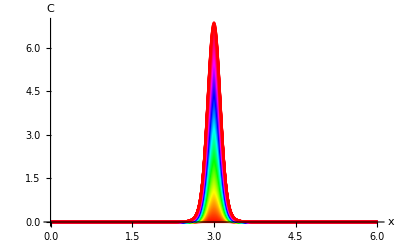

```mathematica
Show[Table[ListPlot[Table[{i*dh,c[i,s]},{i,0,n}],Joined->True,PlotStyle->Hue[s/smax],PlotRange->All],{s,0,smax}],PlotRange->All,AxesLabel->{"x","C"}]
```

```mathematica
plot[s_]:=ListPlot[Table[{i*dh,c[i,s]},{i,0,n}],Joined->True,PlotRange->{{0,6},{0,7}},PlotStyle->{Thick,Hue[s/smax]},AxesLabel->{"x","C"}]
Manipulate[plot[s],{s,0,smax,1}]
```

### 4

```mathematica
Clear[a]
ξ[x_,t_]=H0/(2*a)*x/Sqrt[t];
D[ϕ[ξ[x,t]],t]*D[ξ[x,t],t]==a/H0*D[(1+ϕ[ξ[x,t]]/H0)*D[ϕ[ξ[x,t]],x]*D[ξ[x,t],x],x]//Simplify
```

(H0 (-H0 x^2 ϕ'[(H0 x)/(2 a √t)]+2 t^(3/2) ϕ'[(H0 x)/(2 a √t)]^2+2 t^(3/2) (H0+ϕ[(H0 x)/(2 a √t)]) ϕ''[(H0 x)/(2 a √t)]))/(a t^(3/2))==0

```mathematica
war=D[ϕ[ξ],{ξ,2}]*(1+ϕ[ξ]/a)+2*a*ξ/H0*D[ϕ[ξ],ξ]+1/a*D[ϕ[ξ],ξ]*D[ϕ[ξ],ξ]
```

(2 a ξ ϕ'[ξ])/H0+ϕ'[ξ]^2/a+(1+ϕ[ξ]/a) ϕ''[ξ]

```mathematica
For[i=1,i≤ 10,i++,
For[j=1,j≤ 10,j++,
sol[i,j]=NDSolve[{war==0,ϕ[0]==1,ϕ'[0]==1},ϕ,{ξ,0,20}]/.{a->0.1*i,H0->0.1*j};]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at ξ == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

```mathematica
plot2[i_,j_]:=Plot[Evaluate[{ϕ[ξ]}/.sol[i,j]],{ξ,0,20},PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"ξ","ϕ"}]
Manipulate[plot2[i,j],{i,1,10,1},{j,1,10,1}]
```

```mathematica
For[k=0,k≤ 10,k++,
For[l=1,l≤ 100,l++,
sol2[k,l]=NDSolve[{war==0,ϕ[0]==k,ϕ'[0]==0.1*l},ϕ,{ξ,0,20}]/.{a->0.3,H0->0.6};]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at ξ == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

```mathematica
plot2[k_,l_]:=Plot[Evaluate[{ϕ[ξ]}/.sol2[k,l]],{ξ,0,20},PlotStyle->{Directive[Purple,AbsoluteThickness[3],Dashed]},AxesLabel->{"ξ","ϕ"}]
Manipulate[plot2[k,l],{k,0,10,1},{l,1,100,1}]
```